## Spring-Mass Systems

# Examples Example 3.5

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]]
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap03/mathematica

ClearAll

25 y[x]+y''[x]==18 Sin[10 x]

{{y[x]→C[1] Cos[5 x]+C[2] Sin[5 x]-6/25 Sin[10 x]}}

{y[0]==0,y'[0]==0}

{{y→Function[{x},6/25 (2 Sin[5 x]-Sin[10 x])]}}

True

0

0

{6/25 (2 Sin[5 x]-Sin[10 x])}

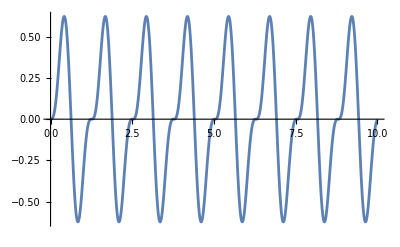

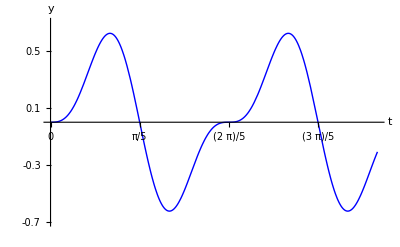

undamped-forced-system.pdf

```mathematica
ClearAll
DE=y''[x]+25y[x]==18 Sin[10x]
DSolve[DE,y[x], x]
ics={y[0]==0, y'[0]==0}
parsol=DSolve[{DE, ics}, y, x]
DE/. parsol[[1]]//Simplify
y[0]/.parsol[[1]]
y'[0]/.parsol[[1]]
y[x]/.parsol
Plot[y[x]/.parsol, {x, 0,10},PlotRange->Automatic]

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12",FontSize->14};
plot:=Plot[y[x]/.parsol,{x,0, 11π/15},PlotRange->{{0, 11π/15},{-0.7,0.7}},AxesLabel->{"t","y"}, PlotStyle->{ {Blue,Thick},  {Red,Thick}, {Red,Thick}},
(*PlotLegends->"Expressions",*)
(*PlotLegends->SwatchLegend[MaTeX[{"y(t) = -\\frac{9}{10}t\\cos(10t) + \\frac{9}{100}\\sin(10t)","a(t)=\\frac{9}{10}\\sqrt{t^2+\\frac{1}{100}}\\approx \\frac{9}{10}|t|"},Magnification->1.5]],    *)
BaseStyle->textStyle, TicksStyle-> Directive[Black,14],Ticks->{{ 0,π/15, 2π/15,3π/15,4π/15,5π/15,6π/15,7π/15,8π/15,9π/15,10π/15}, {-0.7, -0.5, -0.3,-0.1,0.1, 0.3, 0.5, 0.7}}];
plot
Export["undamped-forced-system.pdf",plot]
```

```mathematica
ArgMax[y[x]/.parsol,x]
```

-(142 π)/15

```mathematica
N[y[(2 π)/15]/.parsol[[1]]]
```

0.623538

## Example 3.6

ClearAll

25 y[x]+y''[x]==18 Sin[5 x]

{{y[x]→C[1] Cos[5 x]+C[2] Sin[5 x]-9/50 (10 x Cos[5 x]+Cos[10 x] Sin[5 x]-Cos[5 x] Sin[10 x])}}

{y[0]==0,y'[0]==0}

{{y→Function[{x},-9/50 (10 x Cos[5 x]-Sin[5 x]+Cos[10 x] Sin[5 x]-Cos[5 x] Sin[10 x])]}}

True

0

0

{-9/50 (10 x Cos[5 x]-Sin[5 x]+Cos[10 x] Sin[5 x]-Cos[5 x] Sin[10 x])}

(27 π)/5

(27 π)/5

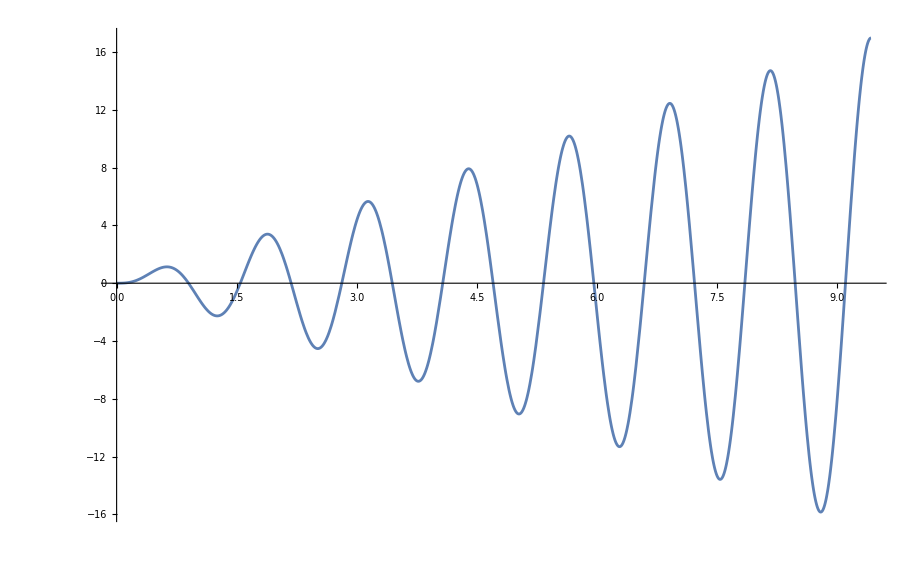

\frac{27 \pi }{5}

```mathematica
ClearAll
DE=y''[x]+25y[x]==18 Sin[5x]
DSolve[DE,y[x], x]
ics={y[0]==0, y'[0]==0}
parsol=DSolve[{DE, ics}, y, x]
DE/. parsol[[1]]//Simplify
y[0]/.parsol[[1]]
y'[0]/.parsol[[1]]
y[x]/.parsol
y[3π]/.parsol[[1]]
Simplify[%]
TeXForm[%]
Plot[y[x]/.parsol, {x, 0,3π},PlotRange->Automatic]
```

```mathematica
<<MaTeX`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap03/mathematica

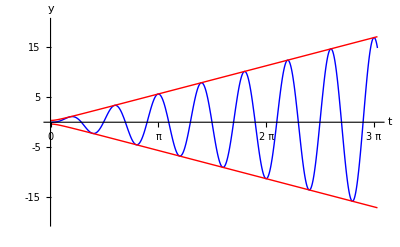

resonance-1.pdf

resonance-1.pdf

```mathematica
f[x_]:= -9/50 (10 x Cos[5 x]-Sin[5 x]+Cos[10 x] Sin[5 x]-Cos[5 x] Sin[10 x]);
g[x_]:=9/5 Sqrt[x^2 +1/25];
h[x_]:=-g[x];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12",FontSize->20};
plot0:=Plot[{f[x],g[x], h[x]},{x,0, 3π+.1},PlotRange->{{0, 3π+.1},{-20,20}}, PlotStyle->{ {Blue,Thick},  {Red,Thick}, {Red,Thick}},
(*PlotLegends->"Expressions",*)
PlotLegends->SwatchLegend[MaTeX[{"y(t) = -\\frac{9}{5}t\\cos(5t) + \\frac{9}{25}\\sin(5t)","a(t)=\\frac{9}{5}\\sqrt{t^2+\\frac{1}{25}}\\approx \\frac{9}{5}|t|"},Magnification->1.5]],    
BaseStyle->textStyle,AxesLabel->{"t","y"},  TicksStyle-> Directive[Black,14],Ticks->{{ 0, π,2π, 3π, 4π}, {-15,-10,  -5, 0, 5, 10, 15}}];
plot0
Export["resonance-1.pdf",plot0]
```

## Example 3.7

```mathematica
Clear[Derivative, x] 
DE=y''[x]+b/10 y'[x]+25y[x]==18 Sin[5x]
DSolve[DE,y[x], x]
ics={y[3π]==27π/5, y'[3π]==0}
parsol=DSolve[{DE, ics}, y[x], x];
DE/. parsol[[1]]//Simplify;
y[3π]/.parsol[[1]]
y'[3π]/.parsol[[1]]
p[x_]=y[x]/.parsol[[1]]
Simplify[%]
TeXForm[%]
p[x]
```

25 y[x]+1/10 b y'[x]+y''[x]==18 Sin[5 x]

{{y[x]→ⅇ^(1/20 (-b-√(-10000+b^2)) x) C[1]+ⅇ^(1/20 (-b+√(-10000+b^2)) x) C[2]-(36 Cos[5 x])/b}}

{y[3 π]==(27 π)/5,y'[3 π]==0}

y[3 π]

y'[3 π]

1/(10 b √(-10000+b^2))9 ⅇ^(-3/20 (-b-√(-10000+b^2)) π-3/20 (-b+√(-10000+b^2)) π) (20 b ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x)-20 √(-10000+b^2) ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x)-20 b ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x)-20 √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x)-3 b^2 ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x) π+3 b √(-10000+b^2) ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x) π+3 b^2 ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x) π+3 b √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x) π-40 √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+3/20 (-b+√(-10000+b^2)) π) Cos[5 x])

(9 ⅇ^(1/20 (√(-10000+b^2) (3 π-x)-b (3 π+x))) (ⅇ^((3 b π)/10) (b (-1+ⅇ^(1/10 √(-10000+b^2) (-3 π+x)))+√(-10000+b^2) (1+ⅇ^(1/10 √(-10000+b^2) (-3 π+x)))) (-20+3 b π)-40 √(-10000+b^2) ⅇ^(1/20 (√(-10000+b^2) (-3 π+x)+b (3 π+x))) Cos[5 x]))/(10 b √(-10000+b^2))

1/(10 b √(-10000+b^2))9 ⅇ^(-3/20 (-b-√(-10000+b^2)) π-3/20 (-b+√(-10000+b^2)) π) (20 b ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x)-20 √(-10000+b^2) ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x)-20 b ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x)-20 √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x)-3 b^2 ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x) π+3 b √(-10000+b^2) ⅇ^(3/20 (-b+√(-10000+b^2)) π+1/20 (-b-√(-10000+b^2)) x) π+3 b^2 ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x) π+3 b √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+1/20 (-b+√(-10000+b^2)) x) π-40 √(-10000+b^2) ⅇ^(3/20 (-b-√(-10000+b^2)) π+3/20 (-b+√(-10000+b^2)) π) Cos[5 x])

\frac{9 \exp \left(\frac{1}{20} \left(\sqrt{b^2-10000} (3 \pi -x)-b (x+3 \pi )\right)\right) \left(e^{\frac{3 \pi  b}{10}} (3 \pi  b-20) \left(b \left(e^{\frac{1}{10} \sqrt{b^2-10000} (x-3 \pi )}-1\right)+\sqrt{b^2-10000}
   \left(e^{\frac{1}{10} \sqrt{b^2-10000} (x-3 \pi )}+1\right)\right)-40 \sqrt{b^2-10000} \cos (5 x) \exp \left(\frac{1}{20} \left(\sqrt{b^2-10000} (x-3 \pi )+b (x+3 \pi )\right)\right)\right)}{10 b \sqrt{b^2-10000}}

ClearAll

250 y[x]+20/3 π y'[x]+10 y''[x]==180 Sin[5 x]

{{y[x]→-(27 Cos[5 x])/(5 π)+ⅇ^(-(π x)/3) C[2] Cos[1/6 √(900-4 π^2) x]+ⅇ^(-(π x)/3) C[1] Sin[1/6 √(900-4 π^2) x]}}

{y[3 π]==(27 π)/5,y'[3 π]==0}

{{y→Function[{x},(27 ⅇ^(-(π x)/3) Sec[1/2 π √(900-4 π^2)] (-ⅇ^((π x)/3) √(225-π^2) Cos[1/2 π √(900-4 π^2)]^3 Cos[5 x]-ⅇ^(π^2) √(225-π^2) Cos[1/2 π √(900-4 π^2)]^2 Cos[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)]^2 Cos[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π Cos[1/2 π √(900-4 π^2)] Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/2 π √(900-4 π^2)] Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]-2 ⅇ^((π x)/3) √(225-π^2) Cos[1/2 π √(900-4 π^2)] Cos[5 x] Sin[1/2 π √(900-4 π^2)]^2-ⅇ^(π^2) √(225-π^2) Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2-ⅇ^(π^2) π Cos[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^3 Cos[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]-ⅇ^(π^2) √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)] Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)] Sin[1/6 √(900-4 π^2) x]-ⅇ^(π^2) π Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^3 Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^((π x)/3) √(225-π^2) Cos[5 x] Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) √(225-π^2) Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x] Tan[1/2 π √(900-4 π^2)]+ⅇ^(π^2) π^2 √(225-π^2) Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x] Tan[1/2 π √(900-4 π^2)]))/(5 π √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))]}}

True

(27 ⅇ^(-π^2) Sec[1/2 π √(900-4 π^2)] (ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)]^3+2 ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]))/(5 π √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))

(27 ⅇ^(-π^2) Sec[1/2 π √(900-4 π^2)] (-1/6 ⅇ^(π^2) π √(900-4 π^2) Cos[1/2 π √(900-4 π^2)]^3+1/6 ⅇ^(π^2) π^3 √(900-4 π^2) Cos[1/2 π √(900-4 π^2)]^3+1/3 ⅇ^(π^2) π √(225-π^2) Cos[1/2 π √(900-4 π^2)]^3-1/3 ⅇ^(π^2) π √(900-4 π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+1/3 ⅇ^(π^2) π^3 √(900-4 π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+2/3 ⅇ^(π^2) π √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2-1/6 ⅇ^(π^2) π √(900-4 π^2) Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]+1/6 ⅇ^(π^2) π^3 √(900-4 π^2) Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]+1/3 ⅇ^(π^2) π √(225-π^2) Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]))/(5 π √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))-(9 ⅇ^(-π^2) Sec[1/2 π √(900-4 π^2)] (ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)]^3+2 ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]))/(5 √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))

{(27 ⅇ^(-(π x)/3) Sec[1/2 π √(900-4 π^2)] (-ⅇ^((π x)/3) √(225-π^2) Cos[1/2 π √(900-4 π^2)]^3 Cos[5 x]-ⅇ^(π^2) √(225-π^2) Cos[1/2 π √(900-4 π^2)]^2 Cos[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)]^2 Cos[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π Cos[1/2 π √(900-4 π^2)] Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/2 π √(900-4 π^2)] Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]-2 ⅇ^((π x)/3) √(225-π^2) Cos[1/2 π √(900-4 π^2)] Cos[5 x] Sin[1/2 π √(900-4 π^2)]^2-ⅇ^(π^2) √(225-π^2) Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2-ⅇ^(π^2) π Cos[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^3 Cos[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]-ⅇ^(π^2) √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)] Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)] Sin[1/6 √(900-4 π^2) x]-ⅇ^(π^2) π Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π^3 Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x]+ⅇ^(π^2) π Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/6 √(900-4 π^2) x] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^((π x)/3) √(225-π^2) Cos[5 x] Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) √(225-π^2) Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x] Tan[1/2 π √(900-4 π^2)]+ⅇ^(π^2) π^2 √(225-π^2) Sin[1/2 π √(900-4 π^2)]^2 Sin[1/6 √(900-4 π^2) x] Tan[1/2 π √(900-4 π^2)]))/(5 π √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))}

{(27 (-Cos[5 x]+(ⅇ^(π^2-(π x)/3) (-1+π^2) (√(225-π^2) Cos[1/3 √(225-π^2) (-3 π+x)]+π Sin[1/3 √(225-π^2) (-3 π+x)]))/(√(225-π^2))))/(5 π)}

(27 ⅇ^(-2 π/3) Sec[1/2 π √(900-4 π^2)] (-ⅇ^(π^2) √(225-π^2) Cos[1/3 √(900-4 π^2)] Cos[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/3 √(900-4 π^2)] Cos[1/2 π √(900-4 π^2)]^2-ⅇ^(2 π/3) √(225-π^2) Cos[10] Cos[1/2 π √(900-4 π^2)]^3-ⅇ^(π^2) π Cos[1/2 π √(900-4 π^2)]^2 Sin[1/3 √(900-4 π^2)]+ⅇ^(π^2) π^3 Cos[1/2 π √(900-4 π^2)]^2 Sin[1/3 √(900-4 π^2)]+ⅇ^(π^2) π Cos[1/3 √(900-4 π^2)] Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/3 √(900-4 π^2)] Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]-ⅇ^(π^2) √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/2 π √(900-4 π^2)] Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]-ⅇ^(π^2) √(225-π^2) Cos[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^2 √(225-π^2) Cos[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2-2 ⅇ^(2 π/3) √(225-π^2) Cos[10] Cos[1/2 π √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2-ⅇ^(π^2) π Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π^3 Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2+ⅇ^(π^2) π Cos[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) π^3 Cos[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^(π^2) √(225-π^2) Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]+ⅇ^(π^2) π^2 √(225-π^2) Sin[1/3 √(900-4 π^2)] Sin[1/2 π √(900-4 π^2)]^2 Tan[1/2 π √(900-4 π^2)]-ⅇ^(2 π/3) √(225-π^2) Cos[10] Sin[1/2 π √(900-4 π^2)]^3 Tan[1/2 π √(900-4 π^2)]))/(5 π √(225-π^2) (Cos[1/2 π √(900-4 π^2)]^2+Sin[1/2 π √(900-4 π^2)]^2) (1+Tan[1/2 π √(900-4 π^2)]^2))

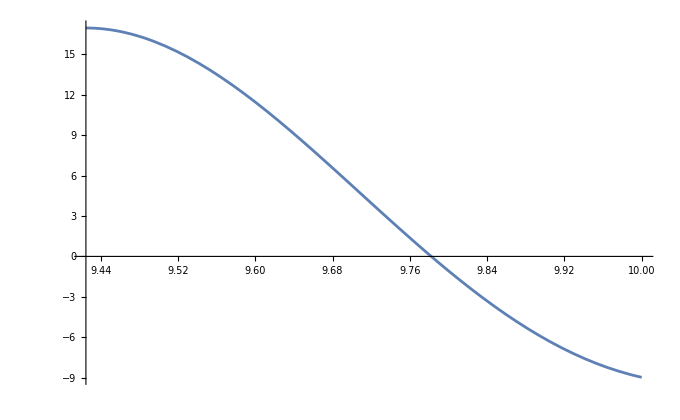

\left\{\frac{27 \left(\frac{\left(\pi ^2-1\right) e^{\pi ^2-\frac{\pi  x}{3}} \left(\pi  \sin \left(\frac{1}{3} \sqrt{225-\pi ^2} (x-3 \pi )\right)+\sqrt{225-\pi ^2} \cos \left(\frac{1}{3} \sqrt{225-\pi ^2} (x-3 \pi
   )\right)\right)}{\sqrt{225-\pi ^2}}-\cos (5 x)\right)}{5 \pi }\right\}

```mathematica
ClearAll
DE=10y''[x]+(20/3π) y'[x]+250y[x]==180 Sin[5x]
DSolve[DE,y[x], x]
icss={y[3π]==(27π)/5, y'[3 π]==0}
parsol=DSolve[{DE, icss}, y, x]
DE/. parsol[[1]]//Simplify
y[3 π]/.parsol[[1]]
y'[3π]/.parsol[[1]]
y[x]/.parsol
Simplify[%]
TeXForm[%]
y[2]/.parsol[[1]]
Plot[y[x]/.parsol, {x,3π ,10},PlotRange->Automatic]
```

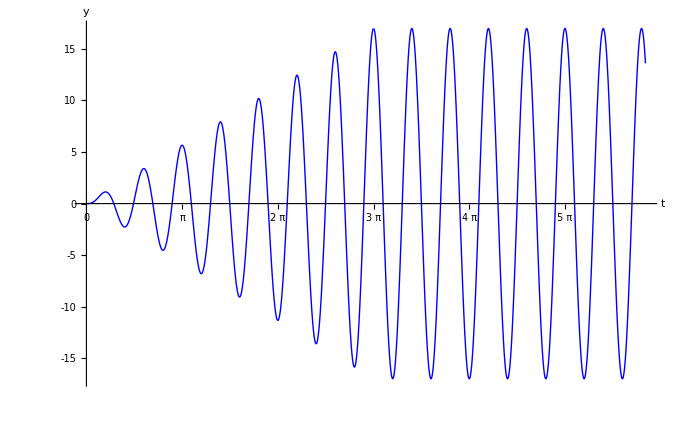

```mathematica
g[x_]:= Piecewise[{{-9/50 (10 x Cos[5 x]-Sin[5 x]+Cos[10 x] Sin[5 x]-Cos[5 x] Sin[10 x]), 0<=x<=3π},{-27/5 π Cos[5 x], 3π<=x}}]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12",FontSize->14};
plot1:=Plot[g[x],{x,0, 6π-0.5},PlotRange->{{0,  6π-.5},{-17,17}}, PlotStyle->{ {Blue,Thick},  {Red,Thick}, {Red,Thick}},
(*PlotLegends->"Expressions",*)
(*PlotLegends->SwatchLegend[MaTeX[{"y(t) = \\begin{cases}
-\\frac{9}{10}t\\cos(10t) + \\frac{9}{100}\\sin(10t) &\\text{ for } 0\\le t<5\\pi/2\\\\
 \\frac{-9}{4} \\pi  \\cos (10 t)& \\text{ for }  t\\ge 5\\pi/2
\\end{cases}"},Magnification->1.5]],*)    
BaseStyle->textStyle, AxesLabel->{"t","y"},TicksStyle-> Directive[Black,14],Ticks->{{ 0, π,2π,3π,4π,5π, 6π, 7π,8π}, {-15,-10,  -5, 0, 5,10,15}}];
plot1
```

```mathematica
Export["resonance-to-sho.pdf",plot1]
```

resonance-to-sho.pdf

## Example 3.8

ClearAll

250 y[x]+0.01 y'[x]+10 y''[x]==180 Sin[5 x]

{{y[x]→ⅇ^(-0.0005 x) C[2] Cos[5. x]-3600. Cos[5. x]+ⅇ^(-0.0005 x) C[1] Sin[5. x]}}

{y[0]==0,y'[0]==0}

{{y→Function[{x},-3600. ⅇ^(-0.0005 x) (-1. Cos[5. x]+1. ⅇ^(0.0005 x) Cos[5. x]-0.0001 Sin[5. x])]}}

1. Sin[5 x]==6.46752×10^-13 ⅇ^(-0.0005 x) Cos[5. x]+1. Sin[5. x]

0.

0.

-3600. ⅇ^(-0.0005 x) (-1. Cos[5. x]+1. ⅇ^(0.0005 x) Cos[5. x]-0.0001 Sin[5. x])

3600. ⅇ^(-0.0005 x) Cos[5. x]-3600. Cos[5. x]+0.36 ⅇ^(-0.0005 x) Sin[5. x]

{-3600. ⅇ^(-0.0005 x) (-1. Cos[5. x]+1. ⅇ^(0.0005 x) Cos[5. x]-0.0001 Sin[5. x])}

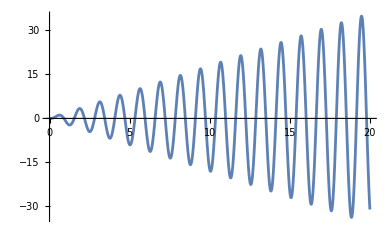

{3599.94}

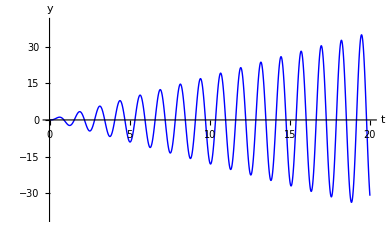

small-damping.pdf

0.36 e^{-0.0005 x} \sin (5. x)+3600. e^{-0.0005 x} \cos (5. x)-3600. \cos (5. x)

```mathematica
ClearAll
DE=10y''[x]+0.01y'[x]+250y[x]==180 Sin[5x]
DSolve[DE,y[x], x]
icss={y[0]==0, y'[0]==0}
parsol=DSolve[{DE, icss}, y, x]
DE/. parsol[[1]]//Simplify
y[0]/.parsol[[1]]
y'[0]/.parsol[[1]]
y[x]/.parsol[[1]]
Simplify[%]
TeXForm[%]
h[x_]=y[x]/.parsol
Plot[y[x]/.parsol, {x,0 ,20},PlotRange->Automatic]
h[7001π]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12",FontSize->14};
plotdamping1:=Plot[h[x],{x,0, 20},PlotRange->{{0,  20},{-40,40}}, PlotStyle->{ {Blue,Thick},  {Red,Thick}, {Red,Thick}},AxesLabel->{"t","y"},
BaseStyle->textStyle, TicksStyle-> Directive[Black,14],Ticks->Automatic];
plotdamping1
Export["small-damping.pdf",plotdamping1]
```

# Example for (beats/near resonance)

```mathematica
ClearAll
DE=y''[x]+5^2 y[x]==18 Cos[γ x]
DSolve[DE,y[x], x]
icss={y[0]==0, y'[0]==0}
parsol=DSolve[{DE, icss}, y, x]
DE/. parsol[[1]]//Simplify
y[0]/.parsol[[1]]
y'[0]/.parsol[[1]]
y[x]/.parsol
Simplify[%]
TeXForm[%]
g[x_]=y[x]/.parsol[[1]]
g[1000]
```

ClearAll

25 y[x]+y''[x]==18 Cos[x γ]

{{y[x]→C[1] Cos[5 x]-(18 Cos[x γ])/(-25+γ^2)+C[2] Sin[5 x]}}

{y[0]==0,y'[0]==0}

{{y→Function[{x},(18 (Cos[5 x]-Cos[x γ]))/(-25+γ^2)]}}

True

0

0

{(18 (Cos[5 x]-Cos[x γ]))/(-25+γ^2)}

{(18 (Cos[5 x]-Cos[x γ]))/(-25+γ^2)}

(18 (Cos[5 x]-Cos[x γ]))/(-25+γ^2)

(18 (Cos[5000]-Cos[1000 γ]))/(-25+γ^2)

\left\{\frac{18 (\cos (5 x)-\cos (\gamma  x))}{\gamma ^2-25}\right\}

# Graphs for a few choices of values of

```mathematica
ClearAll
f[t_,ε_ ]:=-9/((5+ε)ε)Sin[ ε t]*Sin[(5+ε)t]
```

ClearAll

```mathematica
Manipulate[Plot[{f[t,ε],-9/((5+ε)ε)Sin[ ε t],9/((5+ε)ε)Sin[ ε t]},{t,0,30},PlotRange->{{0,30},{-20,20}},AxesLabel->{"t","y"},PlotLabel->StringForm["ε= ``",ε]],{ε, 0.01,0,2,0.1}]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12"};
snap=DynamicModule[{ε=.5},Plot[{f[t,ε],-9/((5+ε)ε)Sin[ ε t],9/((5+ε)ε)Sin[ ε t]},{t,0,25},PlotRange->{{0,25},{-5,5}},AxesLabel->{"t","y"}, PlotStyle->{ {Blue,Normal},  {Red,Thick}, {Red,Thick}},
PlotLabel->StringForm["ε = ``",ε], PlotLegends->Placed[SwatchLegend[MaTeX[{"y(t) = A(t)\\sin\\left((5+\\varepsilon)t\\right)"," y =\pm A(t)"},Magnification->1]],Bottom],
BaseStyle->textStyle, TicksStyle-> Directive[Black,10],Ticks->Automatic ]]
Export["beats.pdf",snap]
```

beats.pdf

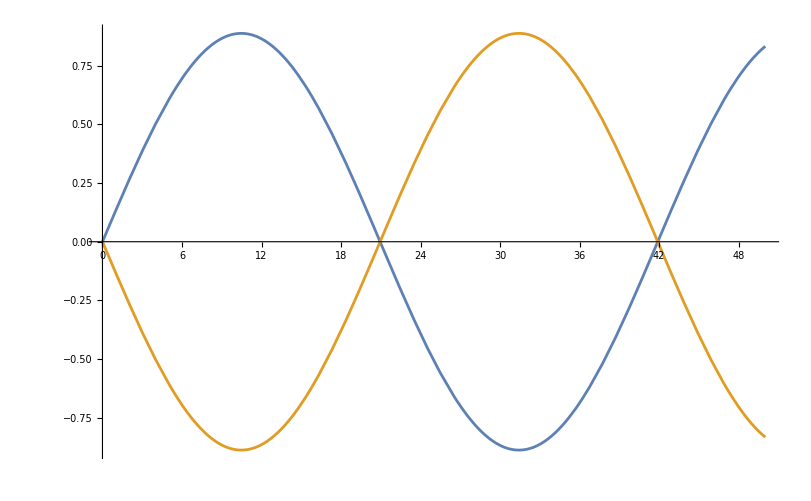

```mathematica
Plot[{18/(20+2 *0.15)*Sin[0.15 t],-18/(20+2 *0.15)*Sin[0.15 t],-18/(20+2 e)Sin[e t]*Sin[1/2(20+2 e)t]},{t,0, 50}]
```

# Calculations

ClearAll

100 y[x]+y''[x]==18 Sin[10.3 x]

{{y[x]→1. C[1] Cos[10. x]+1. C[2] Sin[10. x]-2.95567 Sin[10.3 x]}}

{y[0]==0,y'[0]==0}

{{y→Function[{x},3.04433 Sin[10. x]-2.95567 Sin[10.3 x]]}}

True

0.

-3.55271×10^-15

{3.04433 Sin[10. x]-2.95567 Sin[10.3 x]}

{3.04433 Sin[10. x]-2.95567 Sin[10.3 x]}

3.04433 Sin[10. x]-2.95567 Sin[10.3 x]

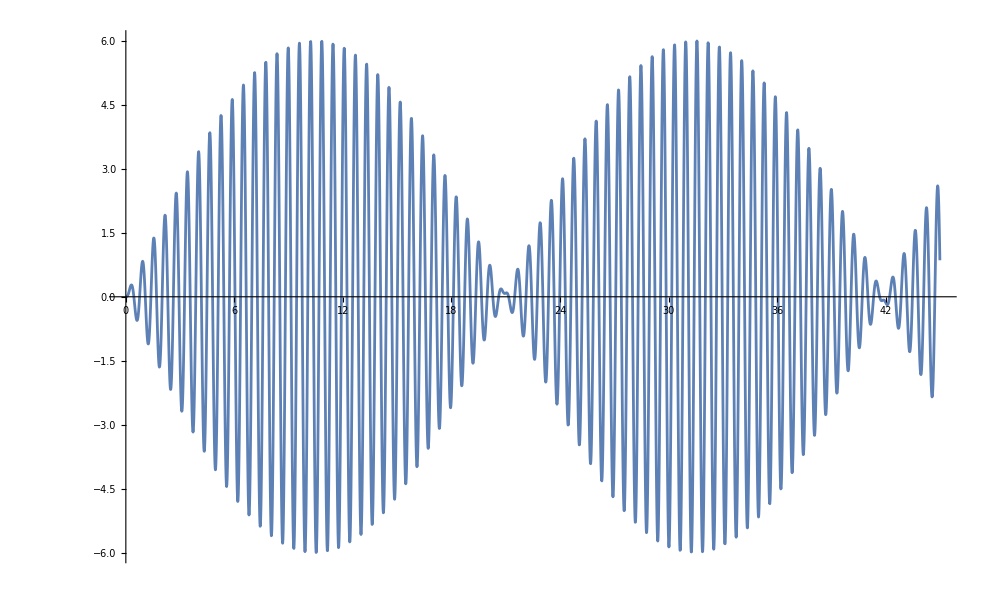

-3.76392

\{3.04433 \sin (10. x)-2.95567 \sin (10.3 x)\}

```mathematica
ClearAll
DE=y''[x]+100 y[x]==18 Sin[10.3x]
DSolve[DE,y[x], x]
icss={y[0]==0, y'[0]==0}
parsol=DSolve[{DE, icss}, y, x]
DE/. parsol[[1]]//Simplify
y[0]/.parsol[[1]]
y'[0]/.parsol[[1]]
y[x]/.parsol
Simplify[%]
TeXForm[%]
g[x_]=y[x]/.parsol[[1]]
Plot[y[x]/.parsol, {x,0,45},PlotRange->Automatic]
g[1000]
```

## 1 (iv)

ClearAll

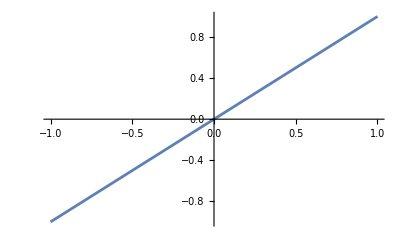

```mathematica
DE=y''[x]+y[x]==x *Sin[x]
```

y[x]+y''[x]==x Sin[x]

```mathematica
{{y[x]->1/8 (-Cos[x]-2 x^2 Cos[x]+Cos[x] Cos[2 x]-2 x Cos[2 x] Sin[x]+2 x Cos[x] Sin[2 x]+Sin[x] Sin[2 x])}}
Plot[y[x], {x, -10,10}]
```

{{y[x]→1/8 (-Cos[x]-2 x^2 Cos[x]+Cos[x] Cos[2 x]-2 x Cos[2 x] Sin[x]+2 x Cos[x] Sin[2 x]+Sin[x] Sin[2 x])}}

-Graphics-

## 1(v)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Sec[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}

{{y[x]→Cos[x] (C[1]+Log[Cos[x]])+(x+C[2]) Sin[x]}}

\{\{y(x)\to (x+c_2) \sin (x)+\cos (x) (\log (\cos (x))+c_1)\}\}

```mathematica
{{y[x]->C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}⟦1,1,2⟧
```

C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]

## 1(vi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Tan[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-ArcTanh[Sin[x]] Cos[x]+C[1] Cos[x]+C[2] Sin[x]}}

{{y[x]→-ArcTanh[Sin[x]] Cos[x]+C[1] Cos[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to c_1 \cos (x)+c_2 \sin (x)+\cos (x) \left(-\tanh ^{-1}(\sin (x))\right)\right\}\right\}

## 1(vii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==(Sin[x])^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/12 (9 Cos[x]^2-Cos[x] Cos[3 x]+4 Sin[x]^4)}}

{{y[x]→1/6 (3+6 C[1] Cos[x]+Cos[2 x]+6 C[2] Sin[x])}}

\left\{\left\{y(x)\to \frac{1}{6} (\cos (2 x)+6 c_1 \cos (x)+6 c_2 \sin (x)+3)\right\}\right\}

## 1(viii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Sec[x] Tan[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ArcTan[Tan[x]] Cos[x]+C[1] Cos[x]-Sin[x]+C[2] Sin[x]-Log[Cos[x]] Sin[x]}}

{{y[x]→ArcTan[Tan[x]] Cos[x]+C[1] Cos[x]+(-1+C[2]-Log[Cos[x]]) Sin[x]}}

\left\{\left\{y(x)\to \cos (x) \tan ^{-1}(\tan (x))+c_1 \cos (x)+\sin (x) (-\log (\cos (x))-1+c_2)\right\}\right\}

## 1(ix)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==(Sec[x])^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-1+C[1] Cos[x]+2 ArcTanh[Tan[x/2]] Sin[x]+C[2] Sin[x]}}

{{y[x]→-1+C[1] Cos[x]+2 ArcTanh[Tan[x/2]] Sin[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to c_1 \cos (x)+c_2 \sin (x)+2 \sin (x) \tanh ^{-1}\left(\tan \left(\frac{x}{2}\right)\right)-1\right\}\right\}

## 1(x)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==Exp[-2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/2 ⅇ^(-2 x) x^2+ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]}}

{{y[x]→1/2 ⅇ^(-2 x) (x^2+2 C[1]+2 x C[2])}}

\left\{\left\{y(x)\to \frac{1}{2} e^{-2 x} \left(x^2+2 c_2 x+2 c_1\right)\right\}\right\}

## 1(xi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+3y'[x]+2y[x]==1/(Exp[x]+1), y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^-x C[2]+ⅇ^(-2 x) (-ⅇ^x+Log[1+ⅇ^x]+ⅇ^x Log[1+ⅇ^x])}}

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x (-1+C[2])+(1+ⅇ^x) Log[1+ⅇ^x])}}

\left\{\left\{y(x)\to e^{-2 x} \left(\left(e^x+1\right) \log \left(e^x+1\right)+(-1+c_2) e^x+c_1\right)\right\}\right\}

```mathematica
Simplify[{{y[x]->ⅇ^(-2 x) C[1]+ⅇ^-x C[2]+ⅇ^(-2 x) (-ⅇ^x+Log[1+ⅇ^x]+ⅇ^x Log[1+ⅇ^x])}}]
```

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x (-1+C[2])+(1+ⅇ^x) Log[1+ⅇ^x])}}

## 1(xii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+3y'[x]+2y[x]==Cos[Exp[x]], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^-x C[2]-ⅇ^(-2 x) Cos[ⅇ^x]}}

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x C[2]-Cos[ⅇ^x])}}

\left\{\left\{y(x)\to e^{-2 x} \left(-\cos \left(e^x\right)+c_2 e^x+c_1\right)\right\}\right\}

```mathematica
Simplify[{{y[x]->ⅇ^(-2 x) C[1]+ⅇ^-x C[2]-ⅇ^(-2 x) Cos[ⅇ^x]}}]
```

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x C[2]-Cos[ⅇ^x])}}

## 1(xiii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==2Cos[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]+1/4 Sin[2 x]}}

{{y[x]→ⅇ^(-2 x) (C[1]+x C[2])+1/4 Sin[2 x]}}

\left\{\left\{y(x)\to \frac{1}{4} \sin (2 x)+e^{-2 x} (c_2 x+c_1)\right\}\right\}

## 1(xiv)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==2Exp[-2x]Cos[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]-1/2 ⅇ^(-2 x) Cos[2 x]}}

{{y[x]→-1/2 ⅇ^(-2 x) (-2 (C[1]+x C[2])+Cos[2 x])}}

\left\{\left\{y(x)\to -\frac{1}{2} e^{-2 x} (\cos (2 x)-2 (c_2 x+c_1))\right\}\right\}

## 2(i)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x y'[x]-y[x]==5, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-5+C[1]/x+x C[2]}}

{{y[x]→-5+C[1]/x+x C[2]}}

\left\{\left\{y(x)\to \frac{c_1}{x}+c_2 x-5\right\}\right\}

## 2(ii)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x y'[x]-y[x]==2x^4, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(2 x^4)/15+C[1]/x+x C[2]}}

{{y[x]→(2 x^4)/15+C[1]/x+x C[2]}}

\left\{\left\{y(x)\to \frac{2 x^4}{15}+c_2 x+\frac{c_1}{x}\right\}\right\}

## 2(iii)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]-x y'[x]+y[x]== x , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→x C[1]+x C[2] Log[x]+1/2 x Log[x]^2}}

{{y[x]→1/2 x (2 C[1]+2 C[2] Log[x]+Log[x]^2)}}

\left\{\left\{y(x)\to \frac{1}{2} x \left(\log ^2(x)+2 c_2 \log (x)+2 c_1\right)\right\}\right\}

```mathematica
Simplify[{{y[x]->x C[1]+x C[2] Log[x]+1/2 x Log[x]^2}}]
```

{{y[x]→1/2 x (2 C[1]+2 C[2] Log[x]+Log[x]^2)}}

## 2(iv)

```mathematica
Clear[Derivative, x]
DSolve[x y''[x]- y'[x]== x , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-x^2/4+(x^2 C[1])/2+C[2]+1/2 x^2 Log[x]}}

{{y[x]→1/4 x^2 (-1+2 C[1])+C[2]+1/2 x^2 Log[x]}}

\left\{\left\{y(x)\to \frac{1}{2} x^2 \log (x)+\frac{1}{4} (-1+2 c_1) x^2+c_2\right\}\right\}